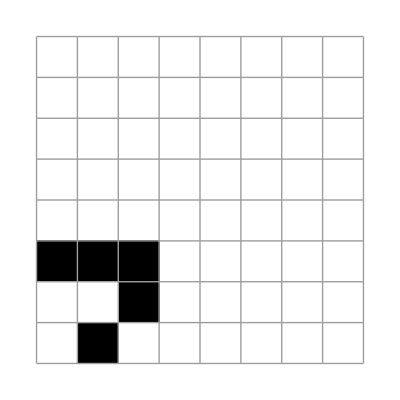

```mathematica
plt=Magnify[ArrayPlot[#,Frame->False,Mesh->True] ,.3]&;
X0=({
    {0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{1,1,1,0,0,0,0,0}
,{0,0,1,0,0,0,0,0}
,{0,1,0,0,0,0,0,0}
});
X0//plt
```

```mathematica
Clear[update];
updateLife[stateXt_]:=Module[
{x,xNW,xN,xNE,xW,xE,xSW,xS,xSE,xPrime,pad}
,
pad=ArrayPad[#,1]&;
x[i_,j_]:=pad[stateXt][[i,j]];
xNW[i_,j_]:=x[i+1,j-1];
xN[i_,j_]:=x[i+1,j];
xNE[i_,j_]:=x[i+1,j+1];
xW[i_,j_]:=x[i,j-1];
xE[i_,j_]:=x[i,j+1];
xSW[i_,j_]:=x[i-1,j-1];
xS[i_,j_]:=x[i-1,j];
xSE[i_,j_]:=x[i-1,j+1];
xPrime[i_,j_]:=Boole[2<xNW[i,j]+xN[i,j]+xNE[i,j]+xW[i,j]+1/2 x[i,j]+xE[i,j]+xSW[i,j]+xS[i,j]+xSE[i,j]<4 ]
;Table[xPrime[i,j] ,{i,2,9},{j,2,9}]
 ];
ListAnimate[plt/@NestList[update,X0,30] ]
```

```mathematica
x[i_,j_]:=X0[[i,j]];
xNW[i_,j_]:=x[i+1,j-1];
xN[i_,j_]:=x[i+1,j];
xNE[i_,j_]:=x[i+1,j+1];
xW[i_,j_]:=x[i,j-1];
xE[i_,j_]:=x[i,j+1];
xSW[i_,j_]:=x[i-1,j-1];
xS[i_,j_]:=x[i-1,j];
xSE[i_,j_]:=x[i-1,j+1];
x[6,2];
xPrime[i_,j_]:=Boole[2<xNW[i,j]+xN[i,j]+xNE[i,j]+xW[i,j]+1/2 x[i,j]+xE[i,j]+xSW[i,j]+xS[i,j]+xSE[i,j]<4 ];
update[stateXt_]:=Module[
{x,xNW,xN,xNE,xW,xE,xSW,xS,xSE,xPrime}
,x[i_,j_]:=stateXt[[i,j]];
xNW[i_,j_]:=x[i+1,j-1];
xN[i_,j_]:=x[i+1,j];
xNE[i_,j_]:=x[i+1,j+1];
xW[i_,j_]:=x[i,j-1];
xE[i_,j_]:=x[i,j+1];
xSW[i_,j_]:=x[i-1,j-1];
xS[i_,j_]:=x[i-1,j];
xSE[i_,j_]:=x[i-1,j+1];
xPrime[i_,j_]:=Boole[2<xNW[i,j]+xN[i,j]+xNE[i,j]+xW[i,j]+1/2 x[i,j]+xE[i,j]+xSW[i,j]+xS[i,j]+xSE[i,j]<4 ]
;Table[xPrime[i,j] ,{i,2,7},{j,2,7}]
 ]
```

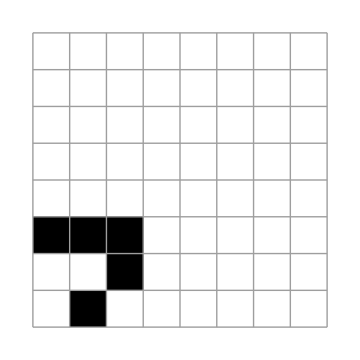

```mathematica
plt=Magnify[ArrayPlot[#,Frame->False,Mesh->True] ,.3]&;
X0=({
    {0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{1,1,1,0,0,0,0,0}
,{0,0,1,0,0,0,0,0}
,{0,1,0,0,0,0,0,0}
});
X0//plt
```